Your Title Here

```mathematica
P=1(*.01325*);(*bar*)
(*Psat[T_]:=10^(5.40221-1838.675/(T+241.263));(*bar*)*)
Psat[T_]:=10^(4.6543-1435.264/(T+208.152));(*bar*)
```

```mathematica
ϕω[ϕ_,T_]:=(18.02/28.97)*ϕ*Psat[T]/P;
(*Vω[T_,T1_]:=-2.114*^-3*(T-T1)-0.0065;*)
(*Vω[T_,T1_]:=-2.571*^-3*(T-T1)-0.02185;*)
Vω[T_,T1_]:=-2.1*^-3*(T-T1)-0.01785;
(*Vω[T_,T1_]:=-2.1*^-3*(T-T1)-0.0065;*)
```

```mathematica
volumePlot=Show[Table[{
Plot[Vω[T,T1],{T,t/.Quiet@FindRoot[ϕω[1,t]==Vω[t,T1],{t,0}],t/.Quiet@FindRoot[-0.0065==Vω[t,T1],{t,0}]},PlotStyle->{Thin,Purple}]
(*Plot[Vω[T,T1],{T,t/.Quiet@FindRoot[ϕω[1,t]==Vω[t,T1],{t,0}],T1},PlotStyle->{Thin,Purple}],
Graphics[Text[Style[NumberForm[0.8+T1/15*0.05,{2,2}],17,Purple,Background->White],{t/.Quiet@FindRoot[Vω[t,T1]==-0.0065,{t,0}],-0.0065}]]*)
},{T1,{0,17.5,35.5,53,70}}(*{T1,0,60,15}*)]];
```

```mathematica
grid=Graphics[{Thin,Gray,
Table[Line[{{T1,0},{T1,ϕω[1,T1]}}],{T1,-10,55,1}],
Table[Line[{{t/.Quiet@FindRoot[ϕω[1,t]==h,{t,15}],h},{55,h}}],{h,0,0.033,0.001}]
}];
```

```mathematica
Manipulate[
Module[{py},
py=ϕω[1,px];

Show[
Plot[ϕω[1,T],{T,-10,55},PlotStyle->RGBColor[0,0.6,0],PlotRange->{{-10,55},{0,0.033}}],
grid,
volumePlot,
Graphics[{
PointSize@0.015,Point[{px,py}],
Text[Style[Column[{Row@{"T = ",px," °C"},Row@{"MC = ",py," kg/kg dry air"}},Alignment->"="],18],Scaled@{0.25,0.8}],
Blue,Point[{{-10,0.0017},{-5,0.0025},{5,0.00542},{15,0.01079},{20,0.0148},{25,0.0202},{30,0.0274},{33.6,0.033}}]
}],
Frame->True,
(*FrameTicks->{{None,All},{All,None}},*)
FrameTicks->{{None,All},{Range[-10,55,5],None}},
LabelStyle->{17,Black},Axes->False,PlotRangeClipping->False,ImagePadding->{{10,75},{95,None}},ImageSize->{610,410}]
],
Grid[{{
Control[{{rh,47,"relative humidity (%)"},10,100,1,Appearance->"Labeled",ImageSize->Small}],
Control[{{DBT,32,"dry bulb temperature (°C)"},10,55,1,Appearance->"Labeled",ImageSize->Small}]
}}],
Control[{{px,-10,"T"},-10,55,1,Appearance->"Labeled"}],
SaveDefinitions->True]
```

```mathematica
0.0017/(-9.2-(-8.4))
```

-0.002125

```mathematica
0.0285/(30.6-44.5)
```

-0.00205036

```mathematica
-0.002125*(-8.4)
```

0.01785

```mathematica
-0.00205*44.5
```

-0.091225

```mathematica
{-10,55}+273
```

{263,328}

```mathematica
Psat[T_]:=10^(4.6543-1435.264/(T+208.152));(*bar*)
```

```mathematica
NumberForm[-64.848+273,6]
```

208.152

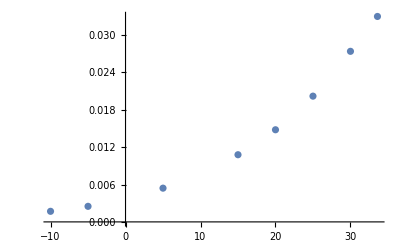

```mathematica
Module[{m1,m2},
m2={{-10,0.0017},{-5,0.0025},{5,0.00542},{15,0.01079},{20,0.0148},{25,0.0202},{30,0.0274},{33.6,0.033}};

ListPlot[m2]
]
```

```mathematica
-0.002571*(-8.5)
```

0.0218535

```mathematica
-2.571*^-3
```

-0.002571

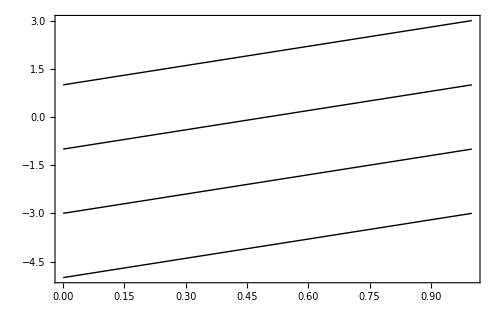

```mathematica
Module[{f},
f[x_,x0_]:=2*(x-x0)+1;

Show[
Plot[f[x,#],{x,0,1},PlotStyle->{Thick,Black}(*,Epilog->Text[Style[#,18,Background->White],{*)]&/@{0,1,2,3},
Axes->False,Frame->True,ImageSize->500,PlotRange->All]
]
```

{{m→0.00180588}}





```mathematica
Solve[-0.02185==-0.0065+m*(-8.5),m]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX